# BTZ Exotic Black Hole Thermodynamics

## Geometrical Definitions and Plotting

First of all, the aim is to calculate the main features of a (2+1) dimention black hole known as the BTZ black hole; that is, to calculate/define the regions of the black hole such as the Ergosphere, the inner and outer event horizon surfaces and the singularity if possible. Recall that, this Black hole is like an upper view of a Kerr (3+1) black hole, so it is expected to not observe any kind of relativistic deformation since this is axis-symmetric. Let’s start with the definitions according the non-negative parameters m,j,l in order to plot a constant time-slice (All in Geometrized units G=h=k_b=1):

```mathematica
Clear[m,j]
SubPlus[r][m_,j_,l_]=√(m*l)√((1+√(1-(j/(m*l))^2))/2);
SubMinus[r][m_,j_,l_]=√(m*l)√((1-√(1-(j/(m*l))^2))/2);
Subscript[r, erg][m_,j_,l_]=√(m*l);
```

Recall on the non-naked singularity condition which states that j<ml so, for furter developments it is taken l=1 in order to reduce the number of parameters and simplify the calculations to show only the important qualitative features. As an example We are going to plot a BTZ BH where m=1.1 and j=1 as follows:

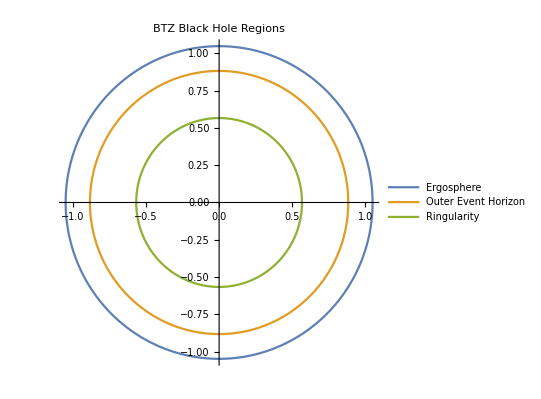

```mathematica
SetDirectory[NotebookDirectory[]];

PolarPlot[{Subscript[r, erg][1.1,1,1],SubPlus[r][1.1,1,1],SubMinus[r][1.1,1,1]},{ϕ,0,2π}, 
		  PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},
		  PlotLabel->Style["BTZ Black Hole Regions",FontSize->22]
		 ]
		 
Export["BTZ.jpeg",PolarPlot[{Subscript[r, erg][1.1,1,1],SubPlus[r][1.1,1,1],SubMinus[r][1.1,1,1]},{ϕ,0,2π}, PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},PlotLabel->Style["BTZ Black Hole Regions",FontSize->22]]];
```

## Thermodynamics for old case:

Recall that old case is the one which does not work for the new mass and angular momentum:

```mathematica
Clear[j]
SubPlus[T][m_,j_,l_]=((SubPlus[r][m,j,l])^2-(SubMinus[r][m,j,l])^2)/(l^2*SubPlus[r][m,j,l]);
SubPlus[Ω][m_,j_,l_]=(SubMinus[r][m,j,l])/(SubPlus[r][m,j,l]);
Subscript[S, old][m_,j_,l_]=(2π)/4 SubMinus[r][m,j,l];
```

Where the corresponding plots are given by:

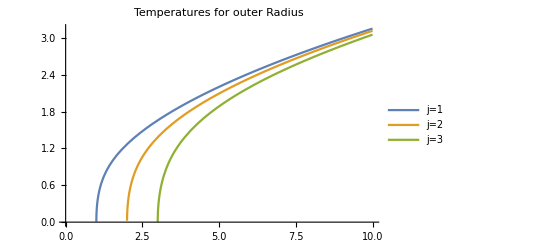

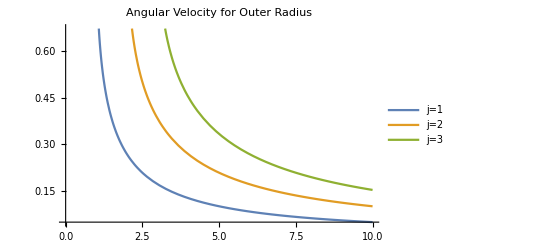

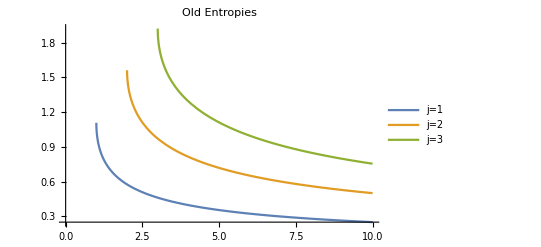

```mathematica
Plot[{SubPlus[T][m,1,1],SubPlus[T][m,2,1],SubPlus[T][m,3,1]},{m,0,10},
	  PlotLabel->Style["Temperatures for outer Radius",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]

Plot[{SubPlus[Ω][m,1,1],SubPlus[Ω][m,2,1],SubPlus[Ω][m,3,1]},{m,0,10},
	  PlotLabel->Style["Angular Velocity for Outer Radius",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]

Plot[{Subscript[S, old][m,1,1],Subscript[S, old][m,2,1],Subscript[S, old][m,3,1]},{m,0,10},
	  PlotLabel->Style["Old Entropies",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]
```

## New Thermodynamics: Bounded Energy case

Now it’s time to use the thermodynamic model constructed by means of the exchange between mass and angular momentum as follows: M=j, J=m. So, by means of this quantities we may compare the difference between the old temperatures and the new ones, where the old are defined by outer event horizon while new ones are defined by the ringularity (Inner event horizon):

```mathematica
Clear[j]
SubMinus[T][m_,j_,l_]=((SubMinus[r][m,j,l])^2-(SubPlus[r][m,j,l])^2)/(l^2*SubMinus[r][m,j,l]);
SubMinus[Ω][m_,j_,l_]=(SubPlus[r][m,j,l])/(SubMinus[r][m,j,l]);
Subscript[S, N][m_,j_,l_]=(2π)/4 SubPlus[r][m,j,l];
```

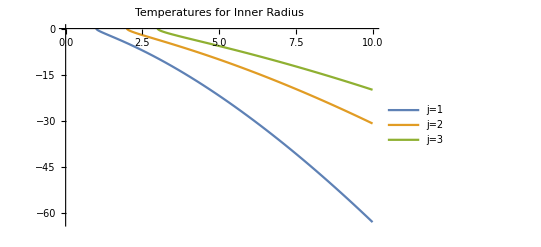

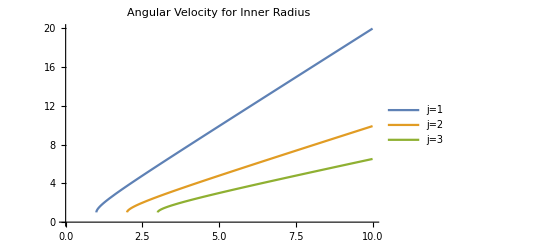

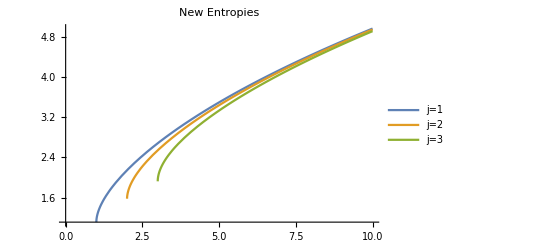

```mathematica
Plot[{SubMinus[T][m,1,1],SubMinus[T][m,2,1],SubMinus[T][m,3,1]},{m,0,10},
	  PlotLabel->Style["Temperatures for Inner Radius",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]
	  
Plot[{SubMinus[Ω][m,1,1],SubMinus[Ω][m,2,1],SubMinus[Ω][m,3,1]},{m,0,10},
	  PlotLabel->Style["Angular Velocity for Inner Radius",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]
	  
Plot[{Subscript[S, N][m,1,1],Subscript[S, N][m,2,1],Subscript[S, N][m,3,1]},{m,0,10},
	  PlotLabel->Style["New Entropies",FontSize->22],
	  PlotLegends->{"j=1","j=2","j=3"}
	  ]
```

## Interesting Feature-Mixing Outer And Inner Properties

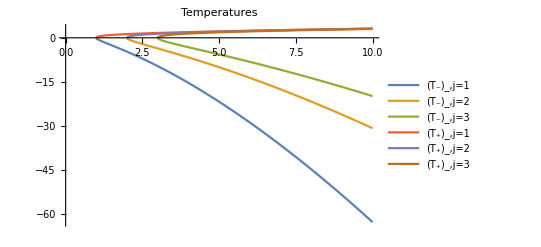

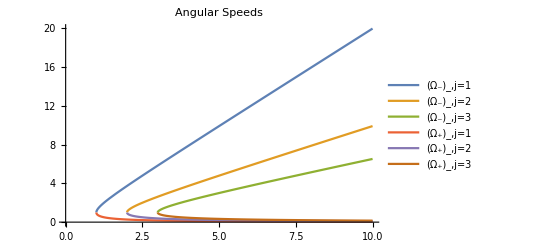

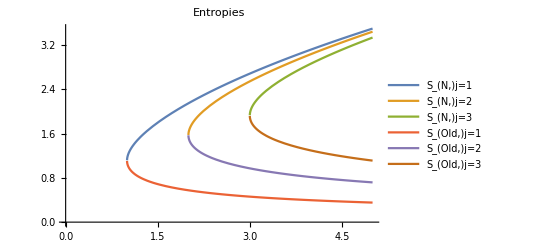

```mathematica
Plot[{SubMinus[T][m,1,1],SubMinus[T][m,2,1],SubMinus[T][m,3,1],SubPlus[T][m,1,1],SubPlus[T][m,2,1],SubPlus[T][m,3,1]},{m,0,10},
	  PlotLabel->Style["Temperatures",FontSize->22],
	  PlotLegends->{"(T_-)_,j=1","(T_-)_,j=2","(T_-)_,j=3","(T_+)_,j=1","(T_+)_,j=2","(T_+)_,j=3"}
	  ]
	  
Plot[{SubMinus[Ω][m,1,1],SubMinus[Ω][m,2,1],SubMinus[Ω][m,3,1],SubPlus[Ω][m,1,1],SubPlus[Ω][m,2,1],SubPlus[Ω][m,3,1]},{m,0,10},
	  PlotLabel->Style["Angular Speeds",FontSize->22],
	  PlotLegends->{"(Ω_-)_,j=1","(Ω_-)_,j=2","(Ω_-)_,j=3","(Ω_+)_,j=1","(Ω_+)_,j=2","(Ω_+)_,j=3"}
	  ]
	  
Plot[{Subscript[S, N][m,1,1],Subscript[S, N][m,2,1],Subscript[S, N][m,3,1],Subscript[S, old][m,1,1],Subscript[S, old][m,2,1],Subscript[S, old][m,3,1]},{m,0,5},
	  PlotLabel->Style["Entropies",FontSize->22],
	  PlotLegends->{"S_(N,)j=1","S_(N,)j=2","S_(N,)j=3","S_(Old,)j=1","S_(Old,)j=2","S_(Old,)j=3"}
	  ]
```

## Accretion Model

Now that We have defined the geometrical Quantities needed to plot the 2D Black hole, it is needed to built an accretion model in order to see how the event horizons behave with time. Let’s star by doing some physical assumptions:

For this Accretion model, We will suppose that the black hole mass increase rate is constant in time, that is dm/dt=c, in order the black hole could have always a source of accreted mass which could incease its area as we expect, and thus, increase the entropy. For simplicity we take the constant factor as c=1 so m=t. Let’s see that this agree with the Quasi-Static condition for inner and outer radius, that is (dr_+)/dm>0 and (dr_-)/dm<0. In the following simulation, j is fixed while m increases; it is clear how the ringularity becomes smaller while event horizon increases so it approaches to ergosphere which turns out to be an equivalent to a Schwarzschild BH

```mathematica
Animate[PolarPlot[{Subscript[r, erg][M,1,1],SubPlus[r][M,1,1],SubMinus[r][M,1,1]},{ϕ,0,2π},
				  PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},
				  PlotLabel->Style["BTZ Black Hole Regions",FontSize->22],
				  PolarAxesOrigin->{0,2},
				  PolarAxes -> True, 
				  PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}},
				  PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}
				 ]
		,{M,1,3}]
		
(*Here we export screenshots of the animation to attach into the Tex file*)
mt1=PolarPlot[{Subscript[r, erg][1,1,1],SubPlus[r][1,1,1],SubMinus[r][1,1,1]},{ϕ,0,2π},PlotLabel->Style["t=0",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
mt2=PolarPlot[{Subscript[r, erg][1.3,1,1],SubPlus[r][1.3,1,1],SubMinus[r][1.3,1,1]},{ϕ,0,2π},PlotLabel->Style["t=0.3",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
mt3=PolarPlot[{Subscript[r, erg][1.6,1,1],SubPlus[r][1.6,1,1],SubMinus[r][1.6,1,1]},{ϕ,0,2π},PlotLabel->Style["t=0.6",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}},PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"}];
Export["mt1.png",mt1];
Export["mt2.png",mt2];
Export["mt3.png",mt3];
```

Let’s suppose that angular momentum increase logarithmically, that means that the angular momentum increases as expected for an accretion disk rotating in the same direction of the black hole, but the logarithm condition imposes an angular speed limit which forces the angular momentum to be always less than mass; as it is mandatory on the condition given by j≤m.  Note that, fixing the mass and increasing slowly the angular momentum, then the ringularity approaches to outer event horizon while ergosphere remains constant and the process stops when singularity is about to be exposed outside event horizon.

```mathematica
Animate[PolarPlot[{Subscript[r, erg][2,1+Log[M],1],SubPlus[r][2,1+Log[M],1],SubMinus[r][2,1+Log[M],1]},{ϕ,0,2π},
				  PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},
				  PlotLabel->Style["BTZ Black Hole Regions",FontSize->22],
				  PolarAxesOrigin->{0,2},
				  PolarAxes -> True, 
				  PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}},
				  PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}
				 ]
		,{M,1,3}]

(*Here we export screenshots of the animation to attach into the Tex file*)
jt1=PolarPlot[{Subscript[r, erg][2,1+Log[1],1],SubPlus[r][2,1+Log[1],1],SubMinus[r][2,1+Log[1],1]},{ϕ,0,2π},PlotLabel->Style["t=0",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
jt2=PolarPlot[{Subscript[r, erg][2,1+Log[2],1],SubPlus[r][2,1+Log[2],1],SubMinus[r][2,1+Log[2],1]},{ϕ,0,2π},PlotLabel->Style["t=1",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
jt3=PolarPlot[{Subscript[r, erg][2,1+Log[3],1],SubPlus[r][2,1+Log[3],1],SubMinus[r][2,1+Log[3],1]},{ϕ,0,2π},PlotLabel->Style["t=2",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}},PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"}];
Export["jt1.png",jt1];
Export["jt2.png",jt2];
Export["jt3.png",jt3];
```

On the other Hand, recall that the cosmological constant impose a minimum value for the angular speed, which impose also a minimum value for angular momentum and thus, a minimum value for the mass m which we set as 1; so joining all these condition we get an angular momentum given by j=1+ln(m) so, the more mass the black hole gains, the slower is the increasing in angular momentum. This model will be taken for the thermodynamic analysis performed

```mathematica
Animate[PolarPlot[{Subscript[r, erg][M,1+Log[M],1],SubPlus[r][M,Log[M]+1,1],SubMinus[r][M,Log[M]+1,1]},{ϕ,0,2π},
				  PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},
				  PlotLabel->Style["BTZ Black Hole Regions",FontSize->22],
				  PolarAxesOrigin->{0,2},
				  PolarAxes -> True, 
				  PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}},
				  PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}
				 ]
		,{M,1,3}]
		
(*Export["Mass Variation.gif",Animate[PolarPlot[{Subscript[r, erg][M,1+Log[M],1],r_+[M,Log[M]+1,1],r_-[M,Log[M]+1,1]},{ϕ,0,2π},
											  PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"},
											  PlotLabel->Style["BTZ Black Hole Regions",FontSize->22],
											  PolarAxesOrigin->{0,2},
											  PolarAxes -> True, 
											  PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}},
											  PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}
											 ]
									,{M,1,3}]
	  ];*)
	  
(*Here we export screenshots of the animation to attach into the Tex file*)
mjt1=PolarPlot[{Subscript[r, erg][1,1+Log[1],1],SubPlus[r][1,1+Log[1],1],SubMinus[r][1,1+Log[1],1]},{ϕ,0,2π},PlotLabel->Style["t=0",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
mjt2=PolarPlot[{Subscript[r, erg][2,1+Log[2],1],SubPlus[r][2,1+Log[2],1],SubMinus[r][2,1+Log[2],1]},{ϕ,0,2π},PlotLabel->Style["t=1",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}}];
mjt3=PolarPlot[{Subscript[r, erg][3,1+Log[3],1],SubPlus[r][3,1+Log[3],1],SubMinus[r][3,1+Log[3],1]},{ϕ,0,2π},PlotLabel->Style["t=2",FontSize->22], PolarAxesOrigin->{0,1.5}, PolarAxes -> True, PolarTicks -> {{0, Pi/4, Pi/2, (3 Pi)/4, Pi, (5 Pi)/4, (3 Pi)/2, (7 Pi)/4}, {0, 0.5, 1, 1.5, 2}}, PolarGridLines -> {{0, Pi/2, Pi, 3 Pi/2}, {0.5, 1, 1.5, 2}},PlotLegends->{"Ergosphere","Outer Event Horizon","Ringularity"}];
Export["mjt1.png",mjt1];
Export["mjt2.png",mjt2];
Export["mjt3.png",mjt3];
```

Another way to visualize is to plot each radius as a 3D surface which gives concentrical cones centered around the time axis:

```mathematica
(*Another Approach to plot the 3D surfaces
RevolutionPlot3D[ r_-[M,1+Log[M],1], {ϕ, 0, 2π}, {M, 1, 10}];
RevolutionPlot3D[ r_+[M,1+Log[M],1], {ϕ, 0, 2π}, {M, 1, 10}];
RevolutionPlot3D[ Subscript[r, erg][M,1+Log[M],1], {ϕ, 0, 2π}, {M, 1, 10}];*)

int=ParametricPlot3D[{SubMinus[r][M,1+Log[M],1]*Cos[ϕ],SubMinus[r][M,1+Log[M],1]*Sin[ϕ], M}, {M, 1, 5}, {ϕ, 0, 2 π},PlotStyle->{Green,Opacity[0.6]}];
evh=ParametricPlot3D[{SubPlus[r][M,1+Log[M],1]*Cos[ϕ],SubPlus[r][M,1+Log[M],1]*Sin[ϕ], M}, {M, 1, 5}, {ϕ, 0, 2 π},PlotStyle->{Orange,Opacity[0.4]}];
ergosph=ParametricPlot3D[{Subscript[r, erg][M,1+Log[M],1]*Cos[ϕ],Subscript[r, erg][M,1+Log[M],1]*Sin[ϕ], M}, {M, 1, 5}, {ϕ, 0, 2 π},PlotStyle->{Blue,Opacity[0.2]}];
Show[int,evh,ergosph]
```

-Graphics3D-

## Temperature, Entropy and Angular Speed time Evolution

Finally, it’s time to go back to our Accretion model in which we are going to use parametrization to see the time-evolution of the features we have already defined:

Let’s first consider the first definitions we had, in which the temperature depended on the external horizon but the entropy depended on the internal horizon; in these we find that, for our accretion model according to the simulation  as there is growth of the BH horizon, the radius of the ringingularity decreases so that,  while the temperature increases, the entropy decreases and even more, the angular speed decreases, as we see:

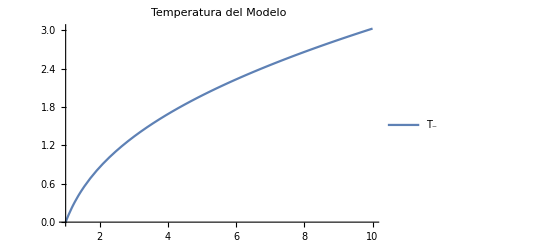

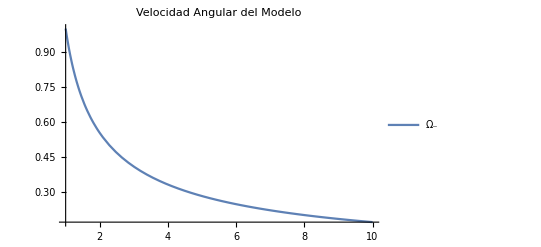

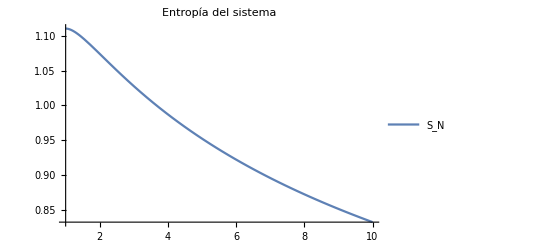

```mathematica
OldModelT=Plot[{SubPlus[T][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Temperatura del Modelo",FontSize->22], PlotLegends->{SubMinus[T]}]
OldModelO=Plot[{SubPlus[Ω][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Velocidad Angular del Modelo",FontSize->22], PlotLegends->{SubMinus[Ω]}]
OldModelS=Plot[{Subscript[S, old][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Entropía del sistema",FontSize->22], PlotLegends->{Subscript[S, N]}]
Export["OldModelT.png",OldModelT];
Export["OldModelO.png",OldModelO];
Export["OldModelS.png",OldModelS];
```

The image that this first thermodynamic approximation gives us is totally inconsisten with the standard interpretation we had about black holes, their horizons and their information storage. To begin with, the growth of a black hole progressively decreases its temperature while here the opposite is observed; on the other hand, entropy is usually associated with information stored on the border of the black hole, that is, on its event horizon, while here the information is stored in the singularity and more and more information is lost since the entropy decreases getting closer and closer to zero. In addition to this, our model considers that the accretion disk contributes to the angular momentum of the black hole as the mass crosses its horizon, however here it also decreases tending to zero. When we relate this with what is exposed in Frenkel, D., Warren, P. B. (2015). Gibbs, Boltzmann, and negative temperatures. American Journal of Physics, 83(2), 163–170 these defective characteristics that we find are related to the same problematic characteristics exhibited by Gibbs entropy which does not fulfill the second thermodynamic law.

Now we are going to adopt the new thermodynamic description in which the entropy is proportional to the area of the external horizon (that is, to the perimeter of the event horizon) while the temperature depends on the surface gravity of the inner horizon (that is, the annular singularity); According to this, the following graphs of temporal evolution are obtained:

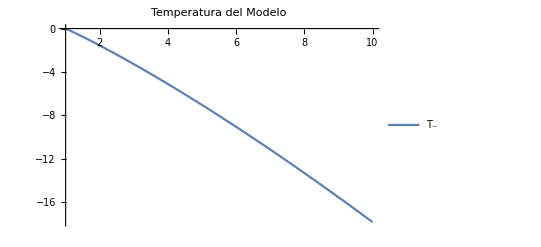

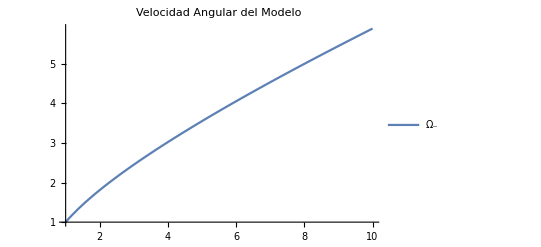

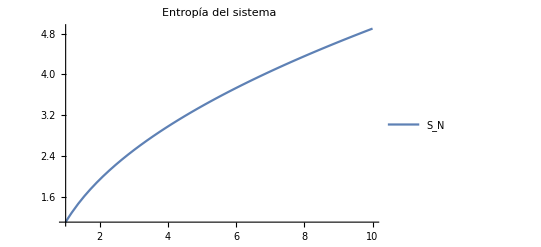

```mathematica
NewModelT=Plot[{SubMinus[T][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Temperatura del Modelo",FontSize->22], PlotLegends->{SubMinus[T]}]
NewModelO=Plot[{SubMinus[Ω][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Velocidad Angular del Modelo",FontSize->22], PlotLegends->{SubMinus[Ω]}]
NewModelS=Plot[{Subscript[S, N][m,1+Log[m],1]},{m,1,10},PlotLabel->Style["Entropía del sistema",FontSize->22], PlotLegends->{Subscript[S, N]}]
Export["NewModelT.png",NewModelT];
Export["NewModelO.png",NewModelO];
Export["NewModelS.png",NewModelS];
```

In this case we can observe that this new perspective is more consistent with the properties thermodynamics expected to be found in the system; the first thing we find is that the second Thermodynamic law is fulfilled in which the mass accretion ratio progressively increases the area of the outer horizon, in the same way the contribution of the angular momentum of the accretion increases the moment of the black hole, now, as expected temperatures are presented negative corresponding to the surface gravity of the singularity. Because they met thermodynamic laws although the system presents negative temperatures, we can associate this definition of entropy with that of Boltzmann for the case of the Spin systems described above.

## Statistical Interpretation

Let' s plot the Helmholtz free energy and the partition function in order to find the amount of available energy:

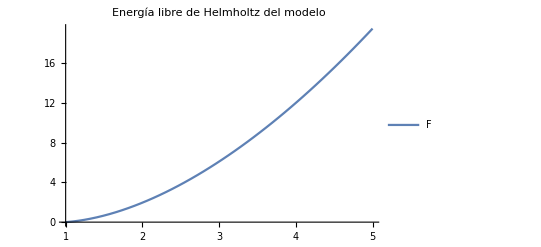

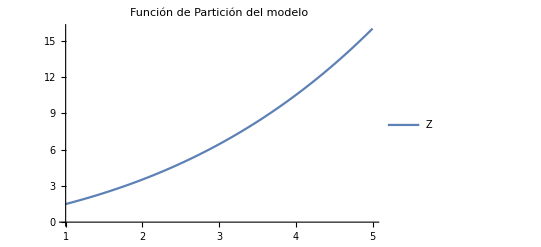

```mathematica
F[m_,j_,l_]=m-(Subscript[S, N][m,j,l]*SubMinus[T][m,j,l])-(SubMinus[Ω][m,j,l]*j);
(*Plot[F[m,1.1,1],{m,1,5}]*)
FF=Plot[F[m,1+Log[m],1],{m,1,5},PlotLabel->Style["Energía libre de Helmholtz del modelo",FontSize->22], PlotLegends->{F}]
ZZ=Plot[Exp[-F[m,1+Log[m],1]/(SubMinus[T][m,1+Log[m],1])],{m,1,5},PlotLabel->Style["Función de Partición del modelo",FontSize->22], PlotLegends->{Z}]
Export["Helmholtz.png",FF];
Export["Part.png",ZZ];
(*Plot[F[m,1+Log[m],1]/m,{m,1,5},PlotLabel->Style["Proporción Energía libre de Helmholtz y Energía entrante al sistema",FontSize->22], PlotLegends->{F}]*)
```